```mathematica
SetDirectory[Directory[]]
```

/Users/jose

```mathematica
krw[Sw_]=(Sw)^2;
kro[Sw_]=(1-Sw)^2;
```

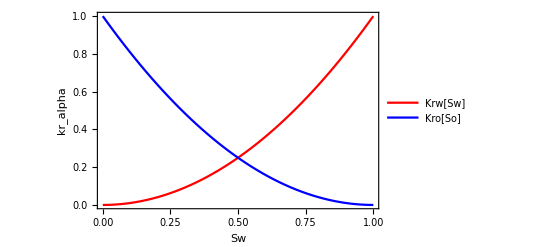

```mathematica
style={{FrameStyle->Directive[Black,16]},{Frame->True}};
Grafico=Plot[{krw[Sw],kro[Sw]},{Sw,0,1},FrameStyle->Directive[Black,16],Frame->True,PlotStyle->{Red, Blue},PlotLegends->{Style["Krw[Sw]",Red],Style["Kro[So]",Blue]},FrameLabel->{Sw,kr_alpha}]
```

```mathematica
Export["OWCuadratic.png",Grafico];
```